```mathematica
(* Referenced from https://github.com/pakreinbold/PDE_Discovery_Weak_Formulation/blob/master/Chaos2019/weight_full.m *)
```

```mathematica
(* freqSpec is a labeling of periodic functions *)
(* 0 -> constant 1 *)
(* 2k+1 -> Sin[πkx] *)
(* 2k -> Cos[πkx] *)
freqSpecToFunc[freqSpec_,x_]:=Simplify[I^Mod[freqSpec+1,2]Exp[I Pi x Quotient[freqSpec+1,2]]//Im//ExpToTrig,x>0]
freqSpecToFunc[#,x]&/@Range[0,5]
```

{1,Sin[π x],Cos[π x],Sin[2 π x],Cos[2 π x],Sin[3 π x]}

```mathematica
(* Calculate (a derivative of) the 1D weight function with the given exponent and frequency component *)
weightFunction[order_,exponent_,freqSpec_]:=weightFunction[order,exponent,freqSpec]=Function[x,Evaluate@D[(x^2-1)^exponent freqSpecToFunc[freqSpec,x]/Factorial[order],{x,order}]]
weightFunction[0,1,0][x]
```

-1+x^2

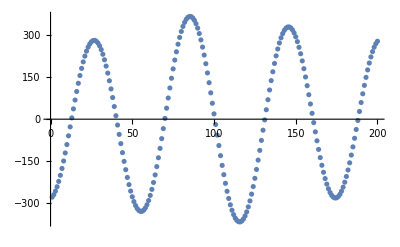

```mathematica
(* Calculate a discretization of the weight function with "size" many points *)
weightEvald[order_,exponent_,freqSpec_,size_]:=weightEvald[order,exponent,freqSpec,size]=N@weightFunction[order,exponent,freqSpec]/@Subdivide[-1,1,size-1]
ListPlot@weightEvald[4,1,5,200]
```

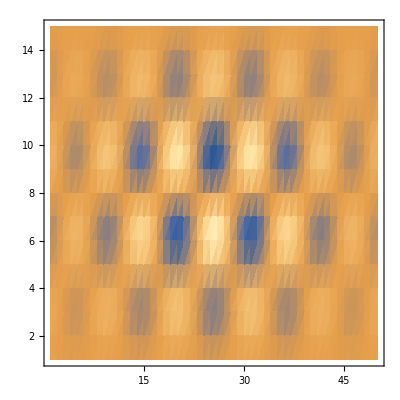

```mathematica
(* To combine multiple 1D weight functions into an nD weight function, take an outer product *)
Outer[Times,weightEvald[0,1,3,15],weightEvald[4,2,8,50]]//ListDensityPlot
```

```mathematica
(* Given a list of different parameters to weightEvald, construct the outer product of all of them *)
weightGrid[specifications_]:=weightGrid[specifications]=Outer@@Prepend[(weightEvald@@#&)/@specifications,Times]
```

```mathematica
traj=Import["C:\\Users\\Sam\\Documents\\GitHub\\kstestproblem\\flowTwithThirdOrder.txt","CSV"];
TensorDimensions@traj
```

{32,2001}

```mathematica
savedArrows=Import["C:\\Users\\Sam\\Documents\\MATLAB\\savedArrows.csv","CSV"]/."NaN"->0;
TensorDimensions@savedArrows
```

{51,800}

```mathematica
(* Pick out random domains *)
integrationDomainSizeX=32;
integrationDomainSizeT=25;
numDomains=100;
(* Give a random starting point for an integration domain *)
randomPart[len_,partSize_]:={#,#+partSize-1}&[RandomInteger[{1,len-(partSize-1)}]]
(* Give a random starting point for an integration domain when there are periodic boundary conditions, so that starting points < partSize away from the end are OK *)
randomPartPeriodicBC[len_,partSize_]:={#,#+partSize-1}&[RandomInteger[{1,len}]]
augmentedPeriodic[xs_,partSize_]:=Join[xs,Take[xs,partSize-1]];
trapz[xs_]:=ListCorrelate[{0.5,0.5},xs]//Total
trapz[xs_]:=Total@xs
```

```mathematica
trajIntegrationDomains={randomPartPeriodicBC[TensorDimensions[traj][[1]],integrationDomainSizeX],randomPart[TensorDimensions[traj][[2]],integrationDomainSizeT]}&/@Range[numDomains];trajDomains=Take@@Flatten[{{augmentedPeriodic[traj,integrationDomainSizeX]},#},1]&/@trajIntegrationDomains;
trajDomains//TensorDimensions
```

{100,32,25}

```mathematica
numArrowSteps=51
arrowData=ArrayReshape[savedArrows,{numArrowSteps,20,20,2}];
TensorDimensions@arrowData
augArrowData=augmentedPeriodic[augmentedPeriodic[#,20]&/@#,20]&/@arrowData;
TensorDimensions@augArrowData
arrowIntegrationDomains={randomPart[numArrowSteps,25],randomPartPeriodicBC[20,20],randomPartPeriodicBC[20,20]}&/@Range[numDomains];
arrowDomains=Transpose[Take@@Flatten[{{augArrowData},#},1]&/@arrowIntegrationDomains,2<->5];
arrowDomains//TensorDimensions
```

51

{51,20,20,2}

{51,39,39,2}

{100,2,20,20,25}

```mathematica
Table[weightGrid[{{1,1,0,2}}],{k,1,15}]
```

{{-2.,2.},{-2.,2.},{-2.,2.},{-2.,2.},{-2.,2.},{-2.,2.},{-2.,2.},{-2.,2.},{-2.,2.},{-2.,2.},{-2.,2.},{-2.,2.},{-2.,2.},{-2.,2.},{-2.,2.}}

```mathematica
Clear[libTerm]
libTerm[factor_,uExp_,derivs_,freqSpecs_,F_,uOnDomain_]:= uOnDomain^uExp factor weightGrid[Transpose@{derivs,F,freqSpecs,TensorDimensions[uOnDomain]}]
libTerm[1,1,{0,0},{3,2},{1,1},trajDomains[[1]]]//TensorDimensions
libTerm[1,1,{0,0,0},{3,4,2},{1,1,1},arrowDomains[[1]][[1]]]//TensorDimensions
```

{32,25}

{20,20,25}

```mathematica
St=2/(0.2 integrationDomainSizeT);
Sx=2/((22/32) integrationDomainSizeX);
Clear[allKSTerms]
termLabels={"timeTerm","advectionTerm","firstOrdTerm","lplTerm","thirdOrdTerm","bilplTerm","constTerm","linTerm","quadTerm","cubicTerm"};
commonExponents={4,3};
allKSTerms[i_,j_,u_]:=Module[
{timeTerm={-St,1,{0,1},{i,j},commonExponents,u},
advectionTerm={Sx/2,2,{1,0},{i,j},commonExponents,u},
firstOrdTerm={-Sx,1,{1,0},{i,j},commonExponents,u},
lplTerm={Sx^2,1,{2,0},{i,j},commonExponents,u},
thirdOrdTerm={-Sx^3,1,{3,0},{i,j},commonExponents,u},
bilplTerm={Sx^4,1,{4,0},{i,j},commonExponents,u},
constTerm={1,0,{0,0},{i,j},commonExponents,u},
linTerm={1,1,{0,0},{i,j},commonExponents,u},
quadTerm={1,2,{0,0},{i,j},commonExponents,u},
cubicTerm={1,3,{0,0},{i,j},commonExponents,u}},
libTerm@@#&/@{timeTerm,advectionTerm,firstOrdTerm,lplTerm,thirdOrdTerm,bilplTerm,constTerm,linTerm,quadTerm,cubicTerm}
]
allKSTerms[2,2,trajDomains[[1]]]//TensorDimensions
```

{10,32,25}

```mathematica
St=2/(0.2 (25));
Sx=2/(20);
Sy=2/(20);
commonExponentsArrow={1,1,1};
termLabels={"timeUTerm","timeVTerm","gradxTerm","gradyTerm","skewCurlxTerm","skewCurlyTerm","lplxTerm","lplyTerm"};
allArrowTerms[i_,j_,k_,arr_]:=Module[
{timeUTerm={-St,1,{1,0,0},{i,j,k},commonExponentsArrow,arr[[1]]},
timeVTerm={-St,1,{0,1,0},{i,j,k},commonExponentsArrow,arr[[2]]},
gradxTerm={-Sx,1,{0,1,0},{i,j,k},commonExponentsArrow,arr[[1]]},
gradyTerm={-Sy,1,{0,0,1},{i,j,k},commonExponentsArrow,arr[[2]]},
skewCurlxTerm={-Sx,1,{0,0,1},{i,j,k},commonExponentsArrow,arr[[1]]},
skewCurlyTerm={-Sy,1,{0,1,0},{i,j,k},commonExponentsArrow,arr[[2]]},
lplxTerm={Sx^2,1,{0,2,0},{i,j,k},commonExponentsArrow,arr[[1]]},
lplyTerm={Sy^2,1,{0,0,2},{i,j,k},commonExponentsArrow,arr[[2]]}
},
Total[(libTerm@@#),-1]&/@{timeUTerm,timeVTerm,gradxTerm,gradyTerm,skewCurlxTerm,skewCurlyTerm,lplxTerm,lplyTerm}
]
allArrowTerms[2,2,2,arrowDomains[[1]]]//TensorDimensions
```

{8}

```mathematica
wtsX={0,1,2,3,4};
wtsT={0,1,2,3,4};
allLibTerms=Flatten[ParallelTable[allKSTerms[i,j,trajDomains[[k]]],{i,1,Length[wtsX]},{j,1,Length[wtsT]},{k,1,numDomains/3}],2];
allLibTerms//TensorDimensions
```

Part::partd: Part specification trajDomains⟦1⟧ is longer than depth of object.

Part::partd: Part specification trajDomains⟦2⟧ is longer than depth of object.

Part::partd: Part specification trajDomains⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification trajDomains⟦1⟧ is longer than depth of object.

Part::partd: Part specification trajDomains⟦2⟧ is longer than depth of object.

Part::partd: Part specification trajDomains⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

{825}

```mathematica
wtsT={0,1,2};
wtsX={0,1,2};
wtsY={0,1,2};
allLibTerms=ParallelTable[allArrowTerms[i,j,k,arrowDomains[[n]]],{i,1,Length[wtsT]},{j,1,Length[wtsX]},{k,1,Length[wtsY]},{n,1,numDomains}];
allLibTerms//TensorDimensions
```

{3,3,3,25,8}

```mathematica
intResults=Flatten[allLibTerms,3];
TensorDimensions@intResults
Export["C:\\Users\\Sam\\Documents\\MATLAB\\intResults.mat",intResults]
```

{675,8}

C:\Users\Sam\Documents\MATLAB\intResults.mat

```mathematica
charSizes=Norm/@Transpose@intResults;
charSizes//MatrixForm
normalizedResults=#/charSizes&/@intResults;
```

(243.788
273.765
68.5061
22.6675
23.7936
68.4412
22.2117
7.53444)

(-0.454639 | 0.890632 | 0.00486897 | 0.00339951 | -0.00145786 | 0.00636323 | -0.000669273 | -4.12341×10^-18
-0.85255 | -0.436024 | 0.15231 | -0.00502045 | -0.0310443 | -0.00546216 | 0.00103806 | 0.242536
-0.143788 | -0.0680479 | -0.983919 | 0.0334909 | 0.0710656 | 0.0000756365 | -0.0206581 | -4.85165×10^-18
0.000268837 | 0.00357243 | 0.0291667 | 0.596253 | 0.128551 | -0.791886 | 0.00315998 | 1.35029×10^-17
0.00488448 | -0.00495309 | 0.00842664 | 0.79245 | -0.248936 | 0.556602 | 0.0113674 | -6.71109×10^-20
-0.213137 | -0.109006 | 0.0380776 | -0.00125511 | -0.00776107 | -0.00136554 | 0.000259516 | -0.970143
-0.0183126 | -0.010312 | 0.0727043 | 0.120509 | 0.946432 | 0.247603 | 0.150698 | -4.26339×10^-17
0.00037332 | 0.00128531 | -0.0320097 | -0.0286889 | -0.140344 | -0.0416134 | 0.988293 | -2.0002×10^-16)

{-4.12341×10^-18,0.242536,-4.85165×10^-18,1.35029×10^-17,-6.71109×10^-20,-0.970143,-4.26339×10^-17,-2.0002×10^-16}

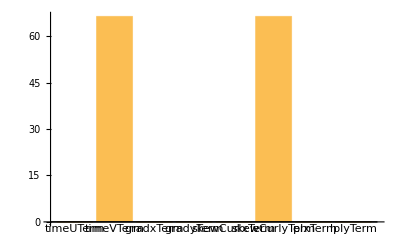

KS Discovered.png

```mathematica
MatrixForm@SingularValueDecomposition[intResults][[3]]
initCoeff=SingularValueDecomposition[intResults,Tolerance->1][[3]][[All,-1]]
chart=BarChart[initCoeff charSizes//Abs,ChartLabels->termLabels,ImageSize->Full]
Export["KS Discovered.png",chart]
```